```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
mub={0,300,400,500,550,575,600};
fitdata=Table[Import["./mub"<>ToString[mub[[i]]]<>".dat"],{i,1,Length[mub]}];
```

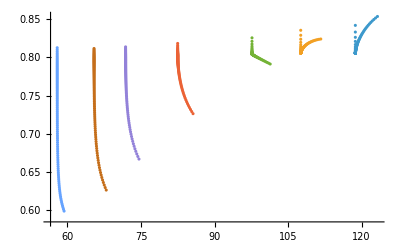

```mathematica
ListPlot[fitdata,PlotRange->All]
```

```mathematica
fitfun=Table[Interpolation[fitdata[[i]]],{i,1,Length[mub]}];
```

```mathematica
T=Table[Flatten[FindRoot[Abs[(fitfun[[i]][x]-0.8)/0.8]==0.01,{x,fitdata[[i]][[90]][[1]],fitdata[[i]][[1]][[1]],fitdata[[i]][[-1]][[1]]}],2][[1]][[2]],{i,1,Length[mub]}]
Export["nu0p01.dat",%];
```

{118.721,107.68,101.184,82.4839,71.8601,65.4293,57.9169}

```mathematica
T=Table[Flatten[FindRoot[Abs[(fitfun[[i]][x]-0.8)/0.8]==0.02,{x,fitdata[[i]][[-1]][[1]],fitdata[[i]][[1]][[1]],fitdata[[i]][[-1]][[1]]}],2][[1]][[2]],{i,1,Length[mub]}]
Export["nu0p02.dat",%];
```

InterpolatingFunction::dmval: 输入值 {123.231} 位于插值函数的数据范围之外. 将使用外推法.

InterpolatingFunction::dmval: 输入值 {111.669} 位于插值函数的数据范围之外. 将使用外推法.

InterpolatingFunction::dmval: 输入值 {101.353} 位于插值函数的数据范围之外. 将使用外推法.

General::stop: 在本次计算中，InterpolatingFunction::dmval 的进一步输出将被抑制.

FindRoot::reged: 点 {101.353} 位于搜索区域 {97.643,101.353} 的边上坐标为 1 的位置处，并且计算搜索方向指向区域外.

FindRoot::reged: 点 {71.8598} 位于搜索区域 {71.8598,74.5905} 的边上坐标为 1 的位置处，并且计算搜索方向指向区域外.

FindRoot::reged: 点 {65.4291} 位于搜索区域 {65.4291,67.9154} 的边上坐标为 1 的位置处，并且计算搜索方向指向区域外.

General::stop: 在本次计算中，FindRoot::reged 的进一步输出将被抑制.

{118.72,108.561,101.353,82.4834,71.8598,65.4291,57.9168}

```mathematica
T=Table[Flatten[FindRoot[Abs[(fitfun[[i]][x]-0.8)/0.8]==0.03,{x,fitdata[[i]][[-1]][[1]],fitdata[[i]][[1]][[1]],fitdata[[i]][[-1]][[1]]}],2][[1]][[2]],{i,1,Length[mub]}]
Export["nu0p03.dat",%];
```

InterpolatingFunction::dmval: 输入值 {123.231} 位于插值函数的数据范围之外. 将使用外推法.

InterpolatingFunction::dmval: 输入值 {111.669} 位于插值函数的数据范围之外. 将使用外推法.

InterpolatingFunction::dmval: 输入值 {101.353} 位于插值函数的数据范围之外. 将使用外推法.

General::stop: 在本次计算中，InterpolatingFunction::dmval 的进一步输出将被抑制.

FindRoot::reged: 点 {101.353} 位于搜索区域 {97.643,101.353} 的边上坐标为 1 的位置处，并且计算搜索方向指向区域外.

FindRoot::reged: 点 {82.4833} 位于搜索区域 {82.4833,85.6177} 的边上坐标为 1 的位置处，并且计算搜索方向指向区域外.

FindRoot::reged: 点 {71.8598} 位于搜索区域 {71.8598,74.5905} 的边上坐标为 1 的位置处，并且计算搜索方向指向区域外.

General::stop: 在本次计算中，FindRoot::reged 的进一步输出将被抑制.

{118.72,111.412,101.353,82.4833,71.8598,65.4291,57.9168}

```mathematica
Export["mub.dat",mub]
```

mub.dat

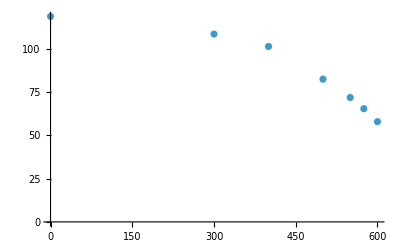

```mathematica
ListPlot[Transpose[{mub,T}],PlotRange->All]
```